```mathematica
NN = 7;
centre = 4;
Commutator[M1_, M2_]:=M1.M2 - M2.M1;
Func[ω_ , t_ ,ϕ_, A_]:= (-I*A)/ω(Sin[ω*t+ϕ] - Sin[ϕ]);
Func2[Aoω_, ϕ_]:= -I*Aoω*Sin[ϕ]*BesselJ[0, Aoω];
```

### Full Chain

#### H_tilde from Dalibard App B (linear full chain oscillation)

```mathematica
HtildeFC [Nl_, centre_, A_, ω_, t_, ϕ_]:=Table[If[Abs[i-j]==1,-Exp[-Func[ω, t, ϕ, A]], 0],{i,1,Nl},{j,1,Nl}];
HtildeFC[NN, centre, A, ω, t, ϕ] // MatrixForm
```

(0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | 0 | 0 | 0 | 0
-ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | 0 | 0 | 0
0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | 0 | 0
0 | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | 0
0 | 0 | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0
0 | 0 | 0 | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω)
0 | 0 | 0 | 0 | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0)

```mathematica
Commutator[HtildeFC[NN, centre, A, ω, t1, ϕ], HtildeFC[NN, centre, A, ω, t2, ϕ]] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

### Single Site Oscillation

#### H (t)

```mathematica
Ht[Nl_, centre_, A_, ω_, t_, ϕ_]:= Table[If[Abs[i-j]==1, -1, If[i==j &&i == centre, A*Cos[ω*t + ϕ], 0]], {i, 1, Nl}, {j, 1, Nl}]
Ht[7, 4, 35, 7, t, Pi/4] // MatrixForm
```

(0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | -1 | 35 Cos[π/4+7 t] | -1 | 0 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
FullSimplify[Commutator[Ht[NN, centre, A, ω, t1, ϕ], Ht[NN, centre, A, ω, t2, ϕ]],Element[ω,Reals] && Element[A, Reals] && Element[ϕ, Reals] && ϕ <= Pi/2 && ϕ >=0  && Element[t1, Reals] && Element[t2, Reals]] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | A (Cos[ϕ+t1 ω]-Cos[ϕ+t2 ω]) | 0 | 0 | 0
0 | 0 | A (-Cos[ϕ+t1 ω]+Cos[ϕ+t2 ω]) | 0 | A (-Cos[ϕ+t1 ω]+Cos[ϕ+t2 ω]) | 0 | 0
0 | 0 | 0 | A (Cos[ϕ+t1 ω]-Cos[ϕ+t2 ω]) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

#### H Tilde

```mathematica
Htilde[Nl_, centre_, A_, ω_, t_, ϕ_]:=Table[If[Abs[i-j]==1, If[i==centre,-Exp[Func[ω, t, ϕ, A]],
If[j==centre, -Exp[-Func[ω, t, ϕ, A]], -1]], 0],{i,1,Nl},{j,1,Nl}];
Htilde[7, 4, A, ω, t, ϕ] // MatrixForm
```

(0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | 0 | 0
0 | 0 | -ⅇ^(-(ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | -ⅇ^(-(ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | 0
0 | 0 | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t ω]))/ω) | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
BesselFac[A_, ω_] := BesselJ[0,A/ω];
Func2[A_, ω_, ϕ_]:= I*A/ω*Sin[ϕ]*BesselJ[0, A/ω];
G[A_, ω_, ϕ_, Nl_, centre_]:=Table[If[Abs[i-j]==1, If[i==centre,-Exp[-Func2[A, ω, ϕ]],
If[j==centre, -Exp[Func2[A, ω, ϕ]], -1]], 0],{i,1,Nl},{j,1,Nl}];
G[A, ω, ϕ, 7, 4] // MatrixForm
(*MatrixExp[A_, ω_,ϕ_]:=MatrixExp[(I*2*π)/ω*)
```

(0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | -ⅇ^((ⅈ A BesselJ[0,A/ω] Sin[ϕ])/ω) | 0 | 0 | 0
0 | 0 | -ⅇ^(-(ⅈ A BesselJ[0,A/ω] Sin[ϕ])/ω) | 0 | -ⅇ^(-(ⅈ A BesselJ[0,A/ω] Sin[ϕ])/ω) | 0 | 0
0 | 0 | 0 | -ⅇ^((ⅈ A BesselJ[0,A/ω] Sin[ϕ])/ω) | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0)

```mathematica
UG[A_, ω_, ϕ_, Nl_, centre_]:=MatrixExp[-I*(2*π)/ω*G[A, ω, ϕ, Nl, centre]];
UG[35, 10, π/2, 7, 4] // MatrixForm
```

(1/4+(ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+(ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | (ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/4+((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(21 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(21 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/4 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2 (2+√2)))+1/4 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2 (2+√2)))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | 1/4+((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]+ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]+ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]])) | ⅇ^(-1/5 ⅈ √2 π)/(4 √2)-ⅇ^(1/5 ⅈ √2 π)/(4 √2)+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2)) | -1/4-1/8 ⅇ^(-1/5 ⅈ √2 π)-1/8 ⅇ^(1/5 ⅈ √2 π)+(ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+(ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (-2+√2))
(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | 1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π)+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π)-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-4 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/8 (1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 (1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | ((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π+7/2 ⅈ BesselJ[0,7/2]))/(4 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π+7/2 ⅈ BesselJ[0,7/2]))/(4 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(4 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(4 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(14 ⅈ BesselJ[0,7/2]) √(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/8 (1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 (1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(14 ⅈ BesselJ[0,7/2]) √(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))) | 1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π)+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π)-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-4 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (2 ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]])+2 (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (2 ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]])+2 (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]])) | ⅇ^(-1/5 ⅈ √2 π)/(4 √2)-ⅇ^(1/5 ⅈ √2 π)/(4 √2)+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))
-1/4+((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/8 (1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 (1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | 1/4+((3+2 √2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((3+2 √2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (7 ⅇ^(7 ⅈ BesselJ[0,7/2])-2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-7 ⅇ^(7 ⅈ BesselJ[0,7/2])+2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/8 √(2+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π) √(ⅇ^(7 ⅈ BesselJ[0,7/2]))+1/8 √(2+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π) √(ⅇ^(7 ⅈ BesselJ[0,7/2]))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/4+((3+2 √2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((3+2 √2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (7 ⅇ^(7 ⅈ BesselJ[0,7/2])-2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-7 ⅇ^(7 ⅈ BesselJ[0,7/2])+2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/8 (1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 (1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | 1/4+((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]+ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]+ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]))
-1/4 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2 (2+√2)))+1/4 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2 (2+√2)))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (2 √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (2 √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | ((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]))/(4 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]))/(4 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])+√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(4 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])+√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(4 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/8 √(2+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2]))+1/8 √(2+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2]))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | 1/4 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π)+1/4 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π)-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(7 ⅈ BesselJ[0,7/2])-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])+√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(4 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-4 ⅇ^(7 ⅈ BesselJ[0,7/2])-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])+√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(4 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/8 √(2+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2]))+1/8 √(2+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2]))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | ((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]))/(4 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]))/(4 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])+√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(4 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])+√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(4 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/4 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2 (2+√2)))+1/4 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2 (2+√2)))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (2 √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (2 √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(7 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))
1/4+((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]+ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]+ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]])) | -1/8 (1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 (1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/4+((3+2 √2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((3+2 √2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (7 ⅇ^(7 ⅈ BesselJ[0,7/2])-2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-7 ⅇ^(7 ⅈ BesselJ[0,7/2])+2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/8 √(2+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π) √(ⅇ^(7 ⅈ BesselJ[0,7/2]))+1/8 √(2+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π) √(ⅇ^(7 ⅈ BesselJ[0,7/2]))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | 1/4+((3+2 √2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((3+2 √2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (7 ⅇ^(7 ⅈ BesselJ[0,7/2])-2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-7 ⅇ^(7 ⅈ BesselJ[0,7/2])+2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/8 (1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 (1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/4+((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])-ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))
ⅇ^(-1/5 ⅈ √2 π)/(4 √2)-ⅇ^(1/5 ⅈ √2 π)/(4 √2)+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2)) | 1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π)+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π)-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-4 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (2 ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]])+2 (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (2 ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]])+2 (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]])) | -1/8 (1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 (1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(14 ⅈ BesselJ[0,7/2]) √(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))) | ((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π+7/2 ⅈ BesselJ[0,7/2]))/(4 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π+7/2 ⅈ BesselJ[0,7/2]))/(4 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(4 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(4 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (2 ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(14 ⅈ BesselJ[0,7/2]) √(2 (2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/8 (1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 (1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-21/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | 1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π)+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π)-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (4 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-4 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(35/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | (ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(21/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (3 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 √2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))
-1/4-1/8 ⅇ^(-1/5 ⅈ √2 π)-1/8 ⅇ^(1/5 ⅈ √2 π)+(ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+(ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (-2+√2)) | ⅇ^(-1/5 ⅈ √2 π)/(4 √2)-ⅇ^(1/5 ⅈ √2 π)/(4 √2)+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2)) | 1/4+((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]+ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (Cos[7 BesselJ[0,7/2]] Cos[14 BesselJ[0,7/2]]-Sin[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]]+ⅈ (Cos[14 BesselJ[0,7/2]] Sin[7 BesselJ[0,7/2]]+Cos[7 BesselJ[0,7/2]] Sin[14 BesselJ[0,7/2]])) | -1/4 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2 (2+√2)))+1/4 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2 (2+√2)))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (2 ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(14 ⅈ BesselJ[0,7/2]) √((2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(21 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | -1/4+((1+√2) ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+((1+√2) ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (3 ⅇ^(7 ⅈ BesselJ[0,7/2])-(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))+(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7 ⅈ BesselJ[0,7/2]) (-3 ⅇ^(7 ⅈ BesselJ[0,7/2])+(2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(21 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(21 ⅈ BesselJ[0,7/2])+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | (ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))+1/8 ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])/(2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-ⅇ^(14 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))+ⅇ^(7 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))) | 1/4+(ⅇ^(-1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))+(ⅇ^(1/5 ⅈ √(2+√2) ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (2+√2))-(ⅇ^(-1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (-2+√2))-(ⅇ^(1/5 ⅈ ⅇ^(-7/2 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) π))/(8 (-2+√2))-1/8 ⅇ^(-1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])-ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))))-1/8 ⅇ^(1/5 ⅈ √2 π-21 ⅈ BesselJ[0,7/2]) (-√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√(2+√2) √(ⅇ^(7 ⅈ BesselJ[0,7/2])) (-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))+2 ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2]))))+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (ⅇ^(14 ⅈ BesselJ[0,7/2])+ⅇ^(7/2 ⅈ BesselJ[0,7/2]) (2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-2 (-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))-√(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])) (√2 ⅇ^(21/2 ⅈ BesselJ[0,7/2])+ⅇ^(7 ⅈ BesselJ[0,7/2]) √(-(-2+√2) ⅇ^(7 ⅈ BesselJ[0,7/2])))))))

```mathematica
FullSimplify[Commutator[Htilde[NN, centre, A, ω, t1, ϕ], Htilde[NN, centre, A, ω, t2, ϕ]],Element[ω,Reals] && Element[A, Reals] && Element[ϕ, Reals] && ϕ <= Pi/2 && ϕ >=0 && Element[t1, Reals] && Element[t2, Reals] ] // MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t1 ω]))/ω)+ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t2 ω]))/ω) | 0 | 0 | 0
0 | 0 | 2 ⅈ Sin[(A (Sin[ϕ+t1 ω]-Sin[ϕ+t2 ω]))/ω] | 0 | 2 ⅈ Sin[(A (Sin[ϕ+t1 ω]-Sin[ϕ+t2 ω]))/ω] | 0 | 0
0 | ⅇ^((ⅈ A (Sin[ϕ]-Sin[ϕ+t1 ω]))/ω)-ⅇ^((ⅈ A (Sin[ϕ]-Sin[ϕ+t2 ω]))/ω) | 0 | -4 ⅈ Sin[(A (Sin[ϕ+t1 ω]-Sin[ϕ+t2 ω]))/ω] | 0 | ⅇ^((ⅈ A (Sin[ϕ]-Sin[ϕ+t1 ω]))/ω)-ⅇ^((ⅈ A (Sin[ϕ]-Sin[ϕ+t2 ω]))/ω) | 0
0 | 0 | 2 ⅈ Sin[(A (Sin[ϕ+t1 ω]-Sin[ϕ+t2 ω]))/ω] | 0 | 2 ⅈ Sin[(A (Sin[ϕ+t1 ω]-Sin[ϕ+t2 ω]))/ω] | 0 | 0
0 | 0 | 0 | -ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t1 ω]))/ω)+ⅇ^((ⅈ A (-Sin[ϕ]+Sin[ϕ+t2 ω]))/ω) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

The code below shows the gauge transformations possible on a Hamiltonian. It shows that for some Hamiltonian G, we can calculate P^†G P and the result will give something that looks like the result we get for the effective Hamiltonian where we have random phases on the hoppings. Basically, we can remove these random phases by using the gauge transformation P. So in a sense we are shaking the middle wannier state by a phase and then if we just redefine this wannier state with this phase, we can remove the overall phases.

```mathematica
P[F_, Nl_, centre_] :=Table[If[i==j, If[i==centre,Exp[-F], 1], 0],{i,1,Nl},{j,1,Nl}];
P[F, 7, 4] // MatrixForm
G2[bess_,  Nl_, centre_]:=Table[If[Abs[i-j]==1, If[i==centre, -bess,
If[j==centre, -bess, -1]], 0],{i,1,Nl},{j,1,Nl}];
G2[B, 7, 4] // MatrixForm
G2PlusHigherOrder[bess_, Nl_, centre_, onsite0_, onsite1_]:= G2[bess, Nl, centre]+ Table[If[i==centre && j == centre, onsite0, If[(j==centre+1 && i == centre+1) || (j==centre-1 && i == centre-1) || (j==centre-1 && i == centre+1) || (j==centre+1 && i == centre-1), onsite1, 0] ], {i,1,Nl},{j,1,Nl}];
G2PlusHigherOrder[B, 7, 4, O0, O1] // MatrixForm
ConjugateTranspose[P[F, 7, 4]].G2PlusHigherOrder[B, 7, 4, O0, O1].P[F,7,4] // MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅇ^-F | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

(0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | -B | 0 | 0 | 0
0 | 0 | -B | 0 | -B | 0 | 0
0 | 0 | 0 | -B | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0)

(0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | O1 | -B | O1 | 0 | 0
0 | 0 | -B | O0 | -B | 0 | 0
0 | 0 | O1 | -B | O1 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0)

(0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | O1 | -B ⅇ^-F | O1 | 0 | 0
0 | 0 | -B ⅇ^(-Conjugate[F]) | ⅇ^(-F-Conjugate[F]) O0 | -B ⅇ^(-Conjugate[F]) | 0 | 0
0 | 0 | O1 | -B ⅇ^-F | O1 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0)

### Triangles

```mathematica
MatrixExp[ⅈ*{{Subscript[x, 1], 0, 0}, {0, Subscript[x, 2], 0}, {0, 0, Subscript[x, 3]}}]
```

{{ⅇ^(ⅈ x_1),0,0},{0,ⅇ^(ⅈ x_2),0},{0,0,ⅇ^(ⅈ x_3)}}

```mathematica
DiagTri[x1_, x2_, x3_]:= FullSimplify[{{x1, 0, 0}, {0, x2, 0}, {0, 0, x3}}, x1 ∈ Reals && x2 ∈ Reals];
DiagTri[e^(ⅈ*a1),e^(ⅈ*a2),e^(ⅈ*a3)]
```

{{e^(ⅈ a1),0,0},{0,e^(ⅈ a2),0},{0,0,e^(ⅈ a3)}}

```mathematica
GenTri[t1_, t2_, t3_, t4_, t5_, t6_]:={{t1, t4, t6}, {t4*, t2, t5},{t6*, t5*,t3}};
GenTri[a, b, c, d, e, f] // MatrixForm
```

(a | d | f
Conjugate[d] | b | e
Conjugate[f] | Conjugate[e] | c)

```mathematica
Conjugate[DiagTri[ⅇ^(ⅈ*a1),ⅇ^(ⅈ*a2),ⅇ^(ⅈ*a3)]]//MatrixForm
FullSimplify[DiagTri[ⅇ^(-ⅈ*a1),ⅇ^(-ⅈ*a2),ⅇ^(-ⅈ*a3)].GenTri[a, b, c, d, f, g].DiagTri[ⅇ^(ⅈ*a1),ⅇ^(ⅈ*a2),ⅇ^(ⅈ*a3)], a1 ∈ Reals && a2 ∈ Reals && a3 ∈ Reals] // MatrixForm
FullSimplify[GenTri[p11, p22, p33, p12, p23, p31]†.GenTri[a11, a22, a33, a12, a23, a31].GenTri[p11, p22, p33, p12, p23, p31]] // MatrixForm
(GenTri[p11, p22, p33, p12, p23, p31]†.GenTri[a11, a22, a33, a12, a23, a31].GenTri[p11, p22, p33, p12, p23, p31])[[0,0]]
mat[[0,0]]
```

(ⅇ^(-ⅈ Conjugate[a1]) | 0 | 0
0 | ⅇ^(-ⅈ Conjugate[a2]) | 0
0 | 0 | ⅇ^(-ⅈ Conjugate[a3]))

(a | d ⅇ^(-ⅈ (a1-a2)) | ⅇ^(-ⅈ (a1-a3)) g
ⅇ^(ⅈ (a1-a2)) Conjugate[d] | b | ⅇ^(-ⅈ (a2-a3)) f
ⅇ^(ⅈ (a1-a3)) Conjugate[g] | ⅇ^(ⅈ (a2-a3)) Conjugate[f] | c)

(p11 (p12 Conjugate[a12]+p31 Conjugate[a31]+a11 Conjugate[p11])+(a22 p12+p31 Conjugate[a23]+a12 Conjugate[p11]) Conjugate[p12]+(a23 p12+a33 p31+a31 Conjugate[p11]) Conjugate[p31] | p12 (p12 Conjugate[a12]+p31 Conjugate[a31]+a11 Conjugate[p11])+p22 (a22 p12+p31 Conjugate[a23]+a12 Conjugate[p11])+(a23 p12+a33 p31+a31 Conjugate[p11]) Conjugate[p23] | a22 p12 p23+a23 p12 p33+a33 p31 p33+p31 (p12 Conjugate[a12]+p23 Conjugate[a23]+p31 Conjugate[a31])+(a12 p23+a11 p31+a31 p33) Conjugate[p11]
p11 p23 Conjugate[a31]+a12 Conjugate[p12]^2+p11 Conjugate[a12] Conjugate[p22]+(a33 p23+a23 Conjugate[p22]) Conjugate[p31]+Conjugate[p12] (a11 p11+p23 Conjugate[a23]+a22 Conjugate[p22]+a31 Conjugate[p31]) | p22 p23 Conjugate[a23]+p12 p23 Conjugate[a31]+a33 p23 Conjugate[p23]+Conjugate[p22] (a22 p22+p12 Conjugate[a12]+a23 Conjugate[p23])+Conjugate[p12] (a11 p12+a12 p22+a31 Conjugate[p23]) | a33 p23 p33+p23^2 Conjugate[a23]+p23 p31 Conjugate[a31]+(a12 p23+a11 p31+a31 p33) Conjugate[p12]+(a22 p23+a23 p33+p31 Conjugate[a12]) Conjugate[p22]
p11 Conjugate[a12] Conjugate[p23]+a31 Conjugate[p31]^2+p11 Conjugate[a31] Conjugate[p33]+Conjugate[p31] (a11 p11+a23 Conjugate[p23]+a33 Conjugate[p33])+Conjugate[p12] (a22 Conjugate[p23]+a12 Conjugate[p31]+Conjugate[a23] Conjugate[p33]) | a23 Conjugate[p23]^2+(a11 p12+a12 p22) Conjugate[p31]+(p22 Conjugate[a23]+p12 Conjugate[a31]) Conjugate[p33]+Conjugate[p23] (a22 p22+p12 Conjugate[a12]+a31 Conjugate[p31]+a33 Conjugate[p33]) | (a22 p23+a23 p33+p31 Conjugate[a12]) Conjugate[p23]+(a12 p23+a11 p31+a31 p33) Conjugate[p31]+(a33 p33+p23 Conjugate[a23]+p31 Conjugate[a31]) Conjugate[p33])

Symbol

Symbol

```mathematica
Symbol::usage
```

Symbol[name] refers to a symbol with the specified name.

```mathematica
Integrate[Cos[A3 * Sin[ω0*t + ϕ] - A2*Sin[2*ω0*t]], {t,-π/ω0,π/ω0}]
```

∫_(-π/ω0)^(π/ω0) Cos[A2 Sin[2 t ω0]-A3 Sin[ϕ+t ω0]]ⅆt

```mathematica
Integrate[Sin[A3 * Sin[ω0*t ]], {t,-π/ω0,π/ω0}]
```

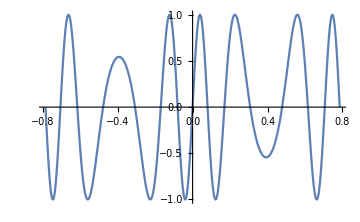
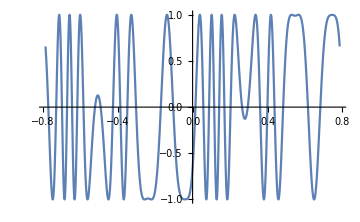

∫_(-π/4)^(π/4) -Sin[7 Cos[12 t]-10 Sin[4 t]]ⅆt

```mathematica
A3T = 10;
A2T = 7;
ω0T = 4;
ϕ3T = π/2;
{Plot[Sin[A3T * Sin[ω0T*t ]], {t,-π/ω0T,π/ω0T}, ImageSize->Medium], Plot[Sin[A3T * Sin[ω0T*t ]- A2T*Sin[3*ω0T*t + ϕ3T]], {t,-π/ω0T,π/ω0T}, ImageSize->Medium]}
Integrate[Sin[A3T * Sin[ω0T*t ]- A2T*Sin[3*ω0T*t + ϕ3T]], {t,-π/ω0T,π/ω0T}]
```

```mathematica
FullSimplify[Integrate[(Sin[ω0*t + ϕ3])^(n-k)*(Sin[2*ω0*t])^k, {t, -π/ω0,π/ω0}],n ∈ Integers && n > -1 && k ∈ Integers && k < n+1&& k > -1 && ω0 ∈ Reals && 1/ω0 ∈ Reals ,ϕ3 ∈ Reals ]
```

FullSimplify::nonopt: Options expected (instead of ϕ3∈) beyond position 2 in FullSimplify[∫_(-π/ω0)^(π/ω0) Sin[2 t ω0]^k Sin[ϕ3+t ω0]^(-k+n)ⅆt,n∈&&n>-1&&k∈&&k<1+n&&k>-1&&ω0∈&&1/ω0∈,ϕ3∈]. An option must be a rule or a list of rules.

FullSimplify[∫_(-π/ω0)^(π/ω0) Sin[2 t ω0]^k Sin[ϕ3+t ω0]^(-k+n)ⅆt,n∈ℤ&&n>-1&&k∈ℤ&&k<1+n&&k>-1&&ω0∈ℝ&&1/ω0∈ℝ,ϕ3∈ℝ]

```mathematica
FullSimplify[Integrate[(Sin[ω0*t ])^(n-k)*(Sin[2*ω0*t])^k, {t, -π/ω0,π/ω0}],n ∈ Integers && n > -1 && k ∈ Integers && k < n+1&& k > -1 && ω0 ∈ Reals && 1/ω0 ∈ Reals ]
```

(((-1/2)^-k (1+(-1)^k+(-1)^n) Gamma[(1+k)/2] Gamma[(1+n)/2])/Gamma[1/2 (2+k+n)]+(-1)^n π ((2^k Gamma[(1+n)/2] Hypergeometric2F1Regularized[k,(1+n)/2,(1+k)/2,1])/Gamma[1/2 (2-k+n)]-(2 √π Hypergeometric2F1Regularized[(1+k)/2,1/2 (2-k+n),(3-k)/2,1])/Gamma[k/2]) Sec[(k π)/2])/(2 ω0)